```mathematica
cwd = NotebookDirectory[];
filepath = cwd <> "trajectory.dat";
trajectory = Import[filepath, "CSV"];
```

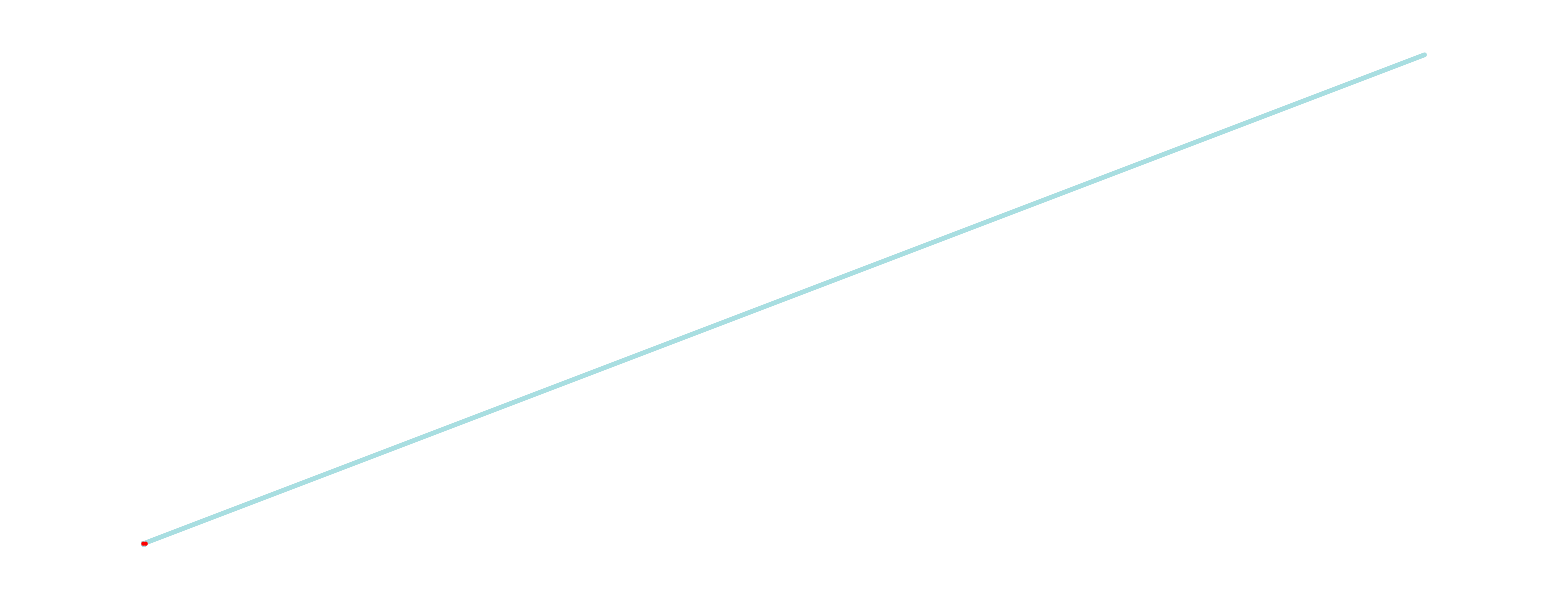

```mathematica
earthToMoonDist = 38440*10^3;
range = earthToMoonDist * 21;
colorscheme = ColorData["CandyColors"];
coloredPoints = Riffle[Point@#&/@trajectory,Table[colorscheme[2 *i/Length@trajectory], {i, 0, Length@trajectory}]];
Graphics[coloredPoints  ~ Join ~ {
Red,
Point[{0,0}],
Point[{r*1.75, 0}]
}, PlotRange->range, ImageSize->Large]
```

```mathematica
schemes = ColorData["Gradients"]
ColorData[#]&/@schemes
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

{ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…],ColorDataFunction[…]}